```mathematica
FF[i_,j_] := FactorialPower[i,j] (* falling factorial with some edge case checking *)
orZ[n_, d_] := If[d >= 1, n/d, 0] (* division that returns 0 instead of undefined for division by 0 *)
(*locs := 100; (* total number of locations in the sea *)
n := 50;       (* a query splits the sea into two pieces, of size n and (locs-n) *)
m := 10;       (* the prior distribution of a ship is uniform over m locations *) *)
probtrue[locs_, n_, m_, inter_] := inter/m (* probability that the query will return true on the various parameters *)
probfalse[locs_, n_, m_, inter_] := 1-probtrue[locs,n,m,inter] (* ... that it will return false *)
vulPrior[locs_,n_,m_,inter_] := 1 / m (* prior vulnerability *)
vulPost[locs_,n_,m_,inter_] := probtrue[locs,n,m,inter] * orZ[1,inter] + probfalse[locs,n,m,inter] * orZ[1, m-inter] (* posteriour vulnerability *)
WCvulPost[locs_,n_,m_,inter_] := If[inter>Min[n,m],1/0,Max[orZ[1,inter],orZ[1,m-inter]]] (* worst case posterior vulnerability; with maximization over outcomes instead of expectation *)
MEDvulPost[locs_,n_,m_,inter_] := If[inter>Min[n,m],1/0,1/Max[inter,m-inter]] (* median vulnerability with median over outcomes instead of expectation *)
probInter[locs_,n_,m_,inter_] := If[inter>n || inter>m || m-inter > locs - n,0,Binomial[m,inter]*FF[n,inter]*FF[locs-n,m-inter]/FF[locs,m]]
(* probabiliy that the size of an intersection is inter; the intersection is between the locations where the query returns true and the locations over which a ship's prior is defined*)
```

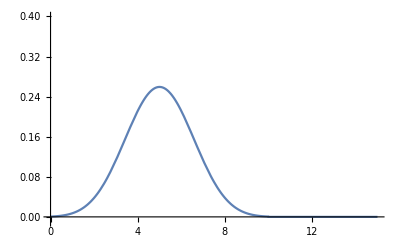

1

```mathematica
Plot[{probInter[100,50,10,i]},{i,0,15},PlotRange->{-0.01,0.4}]
Sum[probInter[100,50,10,i],{i,0,100}]
```

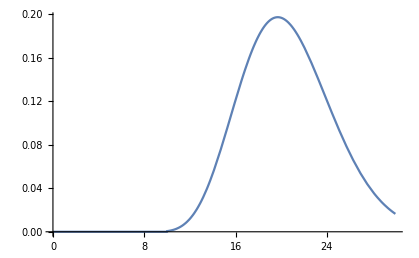

```mathematica
Plot[{probInter[100,50,m,10]},{m,0,30}]
```

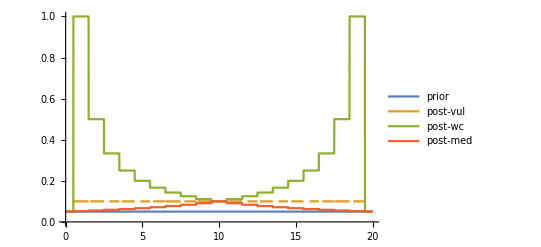

```mathematica
Plot[{
vulPrior[100,50,20,Round[i]],
vulPost[100,50,20,Round[i]],
WCvulPost[100,50,20,Round[i]],
MEDvulPost[100,50,20,Round[i]]
},{i,0,20},PlotLegends->{"prior","post-vul", "post-wc", "post-med"},PlotRange->{0,1}]
```

```mathematica
eVulPrior[locs_,n_,m_]     := Sum[probInter[locs,n,m,i]*vulPrior[locs,n,m,i],{i,0,Min[n,m]}]
eVulPost[locs_,n_,m_]        :=Sum[probInter[locs,n,m,i] * vulPost[locs,n,m,i],{i,0,Min[n,m]}]
eWCVulPost[locs_,n_,m_]   :=Sum[probInter[locs,n,m,i] * WCvulPost[locs,n,m,i],{i,0,Min[n,m]}]
eMEDVulPost[locs_,n_,m_] :=Sum[probInter[locs,n,m,i] * MEDvulPost[locs,n,m,i],{i,0,Min[n,m]}]
```

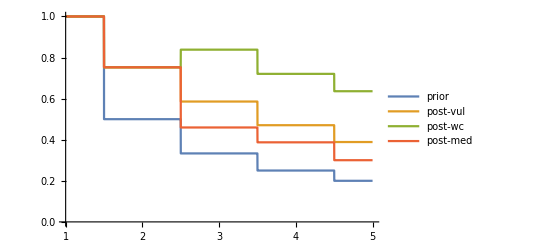

```mathematica
Plot[{
eVulPrior[100,50,Round[m]],
eVulPost[100, 50, Round[m]],
eWCVulPost[100, 50, Round[m]],
eMEDVulPost[100, 50, Round[m]]},
{m,1,5},PlotRange->{0,1},PlotLegends->{"prior","post-vul", "post-wc", "post-med"}]
```

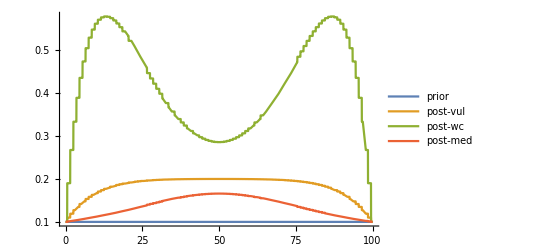

```mathematica
Plot[{
eVulPrior[100,Round[n],10],
eVulPost[100, Round[n], 10],
eWCVulPost[100, Round[n], 10],
eMEDVulPost[100, Round[n], 10]},{n,0,100},PlotLegends->{"prior","post-vul", "post-wc", "post-med"}]
```

```mathematica
Plot3D[{
eVulPrior[100,Round[n],Round[m]],
eVulPost[100, Round[n], Round[m]],
eWCVulPost[100, Round[n], Round[m]],
eMEDVulPost[100, Round[n], Round[m]]},{n,10,90},{m,10,90},
PlotLegends->{"prior","post-vul", "post-wc", "post-med"},AxesLabel->{"n","m"},
MeshFunctions->{#3&},
PlotPoints->20,PlotStyle->Opacity[0.5]]
```

-Graphics3D-